# PHAS2443: Practical Mathematics II Exercises 2: Convolutions and Images

1. This exercise explores the accuracy of approximations to derivatives. Look at the three functions
   a)   Exp[-x]
   b)  Sin[x]
   c)  Log[x]
   and consider their derivatives in the range 0.01<x<2π.
   For each function use graphs to compare 
   i) the exact derivative
   ii) the 'forward difference' approximation, df/dt≈(f(t+δt)-f(t))/δt
   iii) the 'backward difference' approximation, df/dt≈(f(t)-f(t-δt))/δt
   iv) the 'centred difference' approximation,  df/dt≈(f(t+δt)-f(t-δt))/(2 δt).
   Try to use efficient methods for implementing the derivatives.
   Experiment with various values of the finite difference, δt.  Can you draw any general conclusions about the relative accuracies of the one-sided and centred differences?

```mathematica
range = {t, 0.01, 2π} 


(**  Forward/backward/centred difference functions 
	f: Function to differentiate
  t: the variable you want to apply to the function
 dt: the finite difference
**)

forDiff[f_, t_,  dt_] := (f[t + dt] - f[t]) / dt

backDiff[f_, t_,  dt_] := (f[t] - f[t - dt] ) / dt

centDiff[f_,t_,  dt_] := (f[t + dt] - f[t - dt]) / 2dt
```

{t,0.01,2 π}

### Exp[-x]

General::ivar: 0.0101282 is not a valid variable.

General::ivar: 0.138152 is not a valid variable.

General::ivar: 0.266177 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

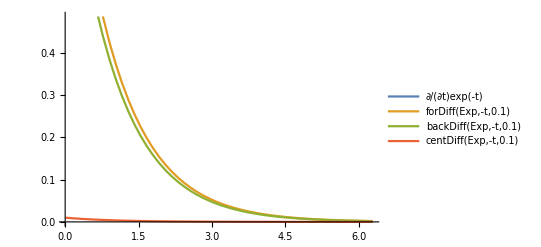

General::ivar: 0.0101282 is not a valid variable.

General::ivar: 0.138152 is not a valid variable.

General::ivar: 0.266177 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

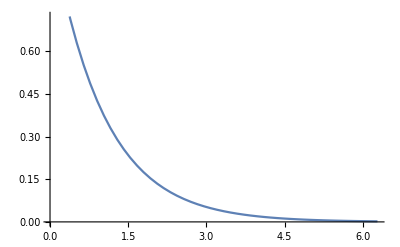

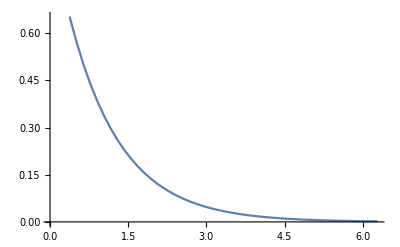

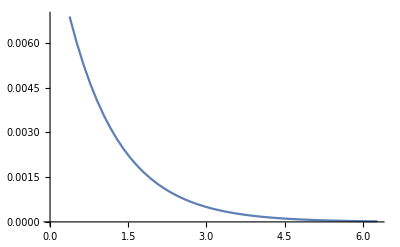

```mathematica
Plot[{D[Exp[-t], t], forDiff[Exp, -t, 0.1], backDiff[Exp, -t, 0.1], centDiff[Exp, -t, 0.1]}, {t, 0.01, 2π}, PlotLegends -> "Expressions"]
Plot[D[Exp[-t], t], {t, 0.01, 2π}]
Plot[forDiff[Exp, -t, 0.1], {t, 0.01, 2π}]
Plot[backDiff[Exp,-t, 0.1], {t, 0.01, 2π}]
Plot[centDiff[Exp,-t, 0.1], {t, 0.01, 2π}]
```

Cos[t]

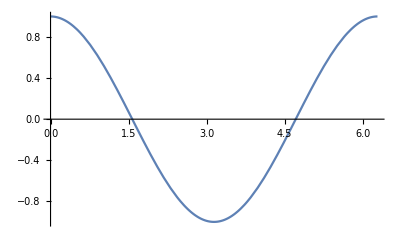

```mathematica
D[Sin[t], t]
Plot[%, {t, 0, 2π}]
```

```mathematica
Plot[D[Sin[t], t], {t, 0, 2π}]
```

General::ivar: 0.000128356 is not a valid variable.

General::ivar: 0.128357 is not a valid variable.

General::ivar: 0.256585 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

### Sin[x]

General::ivar: 0.0101282 is not a valid variable.

General::ivar: 0.138152 is not a valid variable.

General::ivar: 0.266177 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

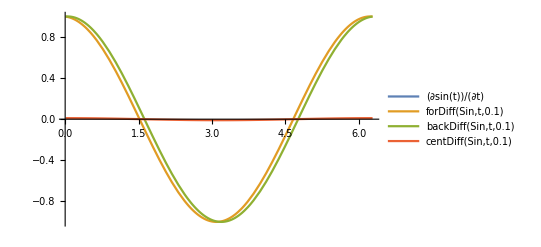

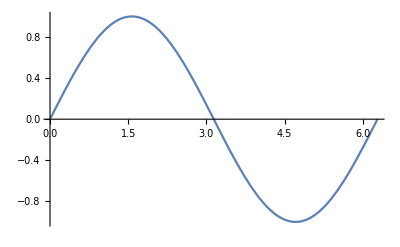

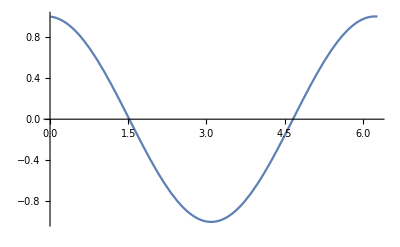

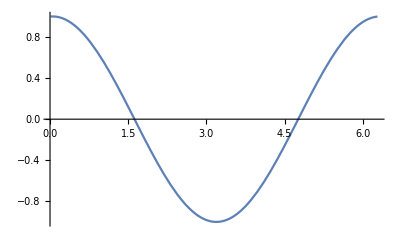

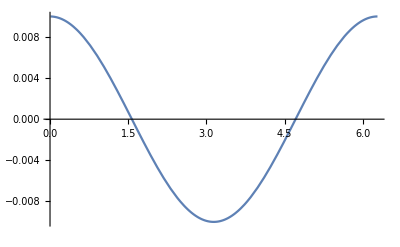

```mathematica
Plot[{D[Sin[t], t], forDiff[Sin, t, 0.1], backDiff[Sin, t, 0.1], centDiff[Sin, t, 0.1]}, {t, 0.01, 2π}, PlotLegends -> "Expressions"]
Plot[D[Sin[t]], {t, 0.01, 2π}]
Plot[forDiff[Sin, t, 0.1], {t, 0.01, 2π}]
Plot[backDiff[Sin,t, 0.1], {t, 0.01, 2π}]
Plot[centDiff[Sin,t, 0.1], {t, 0.01, 2π}]
```

2. This problem involves setting up a simple one-dimensional model of diffusion. Imagine that space is divided up into a finite number of positions, and that on each tick of the clock a particle at any position has a probability p of moving to an adjacent position, with equal probability of moving to the left or to the right. For position i, then, if the numbers of particles at i and its neighbours are  n_(i-1), n_i and n_(i+1),  at the next time step the number of particles at i will be  (p/2 n_(i-1)+(1-p) n_i + p/2 n_(i+1)). We will assume that particles may be divided, and treat the ns as real numbers.  
  Write Mathematica code to model this behaviour, using either RotateRight and RotateLeft or ListConvolve, and apply it to a system of 101 positions, initially empty except for 100 particles in cell 51. With p=0.1, run the sumilation for 500 time steps and plot the result.
   Investigate what happens with the same system when a bias is applied, so that the probability of moving to the right is 0.055 and to the left 0.045.

3. This problem sets up a demonstration of the Rayleigh criterion for the separation of images. The criterion depends on the diffraction pattern of a circular aperture: the intensity in a beam at an angle θ from the normal to an aperture of radius a is
    I(θ)=((2J_1(k a Sin(θ)))/(k a Sin(θ)) )^2 
where k is the wavevector of the light and J_1 is the first order Bessel function of the first kind (BesselJ).
   First create an ideal image. This should be a series of one-unit spikes, at varying spacngs. Create a 255 by 255 grid, with one spike at the centre, and at the corners and  centres of edges of squares, centred on the centre, with edges of lengths 8, 16, 32, 64, 128.
   Now set up a square array, 40 by 40, to represent the blurring arising from this function. Take ka=200, and calculate θ assuming that the image is 2000 units from the aperture, and that the spacing of the mesh is 1 unit. First plot your blur function, then convolve it with the image. 
      Comment on whether your impression of the resulting blurred image is consistent with Rayleigh's criterion, which states that two images can be resolved if their angular separation is greater than 1.22 λ/d where d is the diameter of the aperture and λ is the wavelength.

A.H. Harker
Physics and Astronomy, UCL
January 2008, revised January 2009.